```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Documents\Projects\Thesis\Analysis

```mathematica
ImportTunnelCSV[fname0_]:=Module[{fname=fname0,g},
g=SortBy[GatherBy[Import[fname],#[[2]]&],#[[2]]&];
Map[Map[{#[[1]],#[[3]]}&,#]&,g]
]
```

```mathematica
StatPrune[l0_]:=Module[{l=l0},
Drop[Drop[Sort[l],1],-1]
]
```

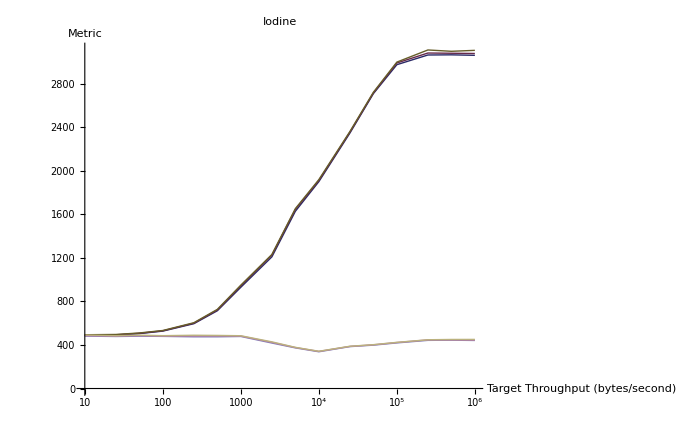

```mathematica
ListLogLinearPlot[Flatten[Map[Transpose,
Map[Map[{
{#[[1]][[1]],Min[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Mean[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Max[StatPrune[Transpose[#][[2]]]]}
}&,GatherBy[#,#[[1]]&]]&,ImportTunnelCSV["E:\\Working\\iodine.10.dlwe.csv"]]
],1],Joined->True,
PlotStyle->Transpose[{Table[Thick,{i,6}],
Join[Thread[Darker[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]],
Thread[Lighter[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]]]
}],
ImageSize->700,PlotLabel->"Iodine",AxesLabel->{"Target Throughput\n(bytes/second)","Metric"},PlotLegend->{"Client-to-Server Min","Client-to-Server Mean","Client-to-Server Max","Server-to-Client Min","Server-to-Client Mean","Server-to-Client Max"},LegendPosition->{0.4,-0.2},LegendSize->{0.6,0.3}]
```

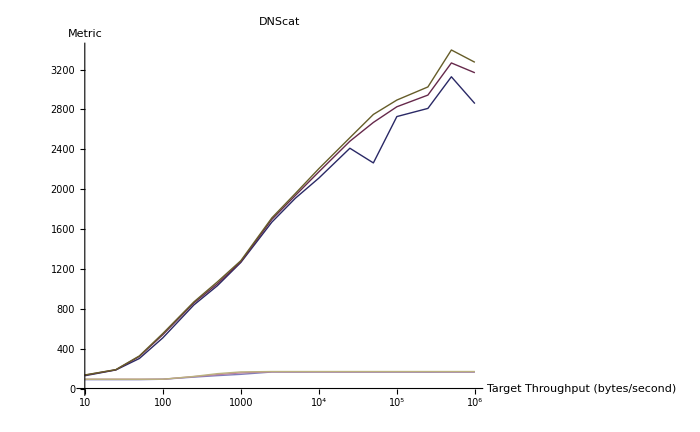

```mathematica
ListLogLinearPlot[Flatten[Map[Transpose,
Map[Map[{
{#[[1]][[1]],Min[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Mean[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Max[StatPrune[Transpose[#][[2]]]]}
}&,GatherBy[#,#[[1]]&]]&,ImportTunnelCSV["E:\\Working\\dnscat.10.dlwe.csv"]]
],1],Joined->True,
PlotStyle->Transpose[{Table[Thick,{i,6}],
Join[Thread[Darker[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]],
Thread[Lighter[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]]]
}],
ImageSize->700,PlotLabel->"DNScat",AxesLabel->{"Target Throughput\n(bytes/second)","Metric"},PlotLegend->{"Client-to-Server Min","Client-to-Server Mean","Client-to-Server Max","Server-to-Client Min","Server-to-Client Mean","Server-to-Client Max"},LegendPosition->{0.4,-0.2},LegendSize->{0.6,0.3}]
```

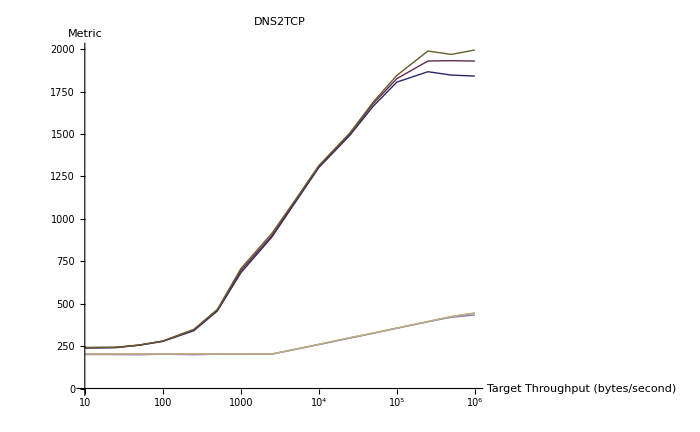

```mathematica
ListLogLinearPlot[Flatten[Map[Transpose,
Map[Map[{
{#[[1]][[1]],Min[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Mean[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Max[StatPrune[Transpose[#][[2]]]]}
}&,GatherBy[#,#[[1]]&]]&,ImportTunnelCSV["E:\\Working\\dns2tcp.10.dlwe.csv"]]
],1],Joined->True,
PlotStyle->Transpose[{Table[Thick,{i,6}],
Join[Thread[Darker[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]],
Thread[Lighter[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]]]
}],
ImageSize->700,PlotLabel->"DNS2TCP",AxesLabel->{"Target Throughput\n(bytes/second)","Metric"},PlotLegend->{"Client-to-Server Min","Client-to-Server Mean","Client-to-Server Max","Server-to-Client Min","Server-to-Client Mean","Server-to-Client Max"},LegendPosition->{0.4,-0.2},LegendSize->{0.6,0.3}]
```

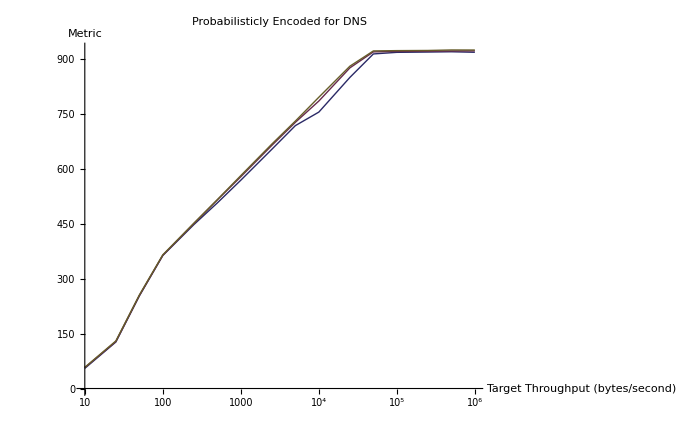

```mathematica
ListLogLinearPlot[Flatten[Map[Transpose,
Map[Map[{
{#[[1]][[1]],Min[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Mean[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Max[StatPrune[Transpose[#][[2]]]]}
}&,GatherBy[#,#[[1]]&]]&,ImportTunnelCSV["E:\\Working\\prob-dns.10.dlwe.csv"]]
],1],Joined->True,
PlotStyle->Transpose[{Table[Thick,{i,6}],
Join[Thread[Darker[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]],
Thread[Lighter[{RGBColor[0.24720000000000014,0.24,0.6],RGBColor[0.6,0.24,0.4428931686004542],RGBColor[0.6,0.5470136627990908,0.24]}]]]
}],
ImageSize->700,PlotLabel->"Probabilisticly Encoded for DNS",AxesLabel->{"Target Throughput\n(bytes/second)","Metric"},PlotLegend->{"Client-to-Server Min","Client-to-Server Mean","Client-to-Server Max","Server-to-Client Min","Server-to-Client Mean","Server-to-Client Max"},LegendPosition->{0.4,-0.2},LegendSize->{0.6,0.3}]
```